```mathematica
Clear[optionsselect,bandPlotWithWeight]
optionsselect[options:Sequence[___Rule]][func_Symbol] := optionsselect[options, func];
optionsselect[options:Sequence[___Rule], func_Symbol] := Sequence @@ FilterRules[{options}, Options[func]];
optionsselect[options:Sequence[___Rule], func_Symbol, optionnamestoadd:{__}] := Sequence @@ FilterRules[{options}, {Options[func], optionnamestoadd}];

Options[bandPlotWithWeight] = Join[Options[Graphics], Options[BarLegend],
	{Joined -> True, ColorFunction -> (Hue[2(1 - #)/3] &), PlotStyle -> Sequence[Thick, PointSize[.02]], "LegendTickDigits" -> {3, 4}, "LegendPosition" -> Right, "TickLabels" -> None}];
(*bandPlotWithWeight[banddatawithstate_,cfunc_,cname_String,joined_:(True|False),ps:OptionsPattern[Graphics]]:=*)
bandPlotWithWeight[banddatawithweight_,
				   hisymmptname : {(_String|OverBar[_String])..} : {""},
				   ptsnumbers : {_?NumericQ..} : {1},
				   yticks :{{_, _}..} : Automatic,
				   ps:OptionsPattern[]] :=
Module[{kbdat, colors, m, n, lines, bfig, legend, fontfamily = (*"Helvetica"*)(*"Times New Roman"*)"Arial", style,
		style2, bdat, cdat, cfunc = OptionValue[ColorFunction], dticks, frameticks, ps1, ps2},
	{bdat, cdat} = Transpose[banddatawithweight, {3, 2, 1}]; {m, n} = Dimensions[bdat];
	dticks = {ptsnumbers, hisymmptname}ᵀ; frameticks = {{(*Automatic*)yticks, None}, {dticks, None}};
	style = {FontSize -> 17, FontFamily -> fontfamily}; style2 = Directive[Black(*,Thick*)];
	kbdat = Transpose[{ConstantArray[(*kdat*)Range[n], m], bdat}, {3, 1, 2}];
	colors = Map[cfunc, Rescale @ cdat, {2}];
	lines = MapThread[If[OptionValue[Joined], Line, Point][#, VertexColors -> #2] &, {kbdat, colors}];
	(*ps1 = Sequence @@ FilterRules[{ps}, Options[Graphics]]; ps2 = Sequence @@ FilterRules[{ps}, Options[BarLegend]];*)
	ps1 = (*TBMethod`DataVisualization`Private`*)optionsselect[ps, Graphics];
	ps2 = (*TBMethod`DataVisualization`Private`*)optionsselect[ps, BarLegend, {"TickLabels"(*->None*)}];
	bfig = Graphics[{OptionValue[PlotStyle], lines}, ps1, GridLines -> {ptsnumbers, Automatic}, PlotRangeClipping -> True, (*AspectRatio -> GoldenRatio,*) FrameTicks -> frameticks, 
					 Frame -> True, FrameLabel -> {None, "\!\(\*SubscriptBox[\(E\), \(\)]\)"}, FrameTicksStyle -> style2, FrameStyle -> style2, LabelStyle -> style2, BaseStyle -> style];
	legend = BarLegend[{cfunc, {0, 1}}, ps2, 
					(*"Ticks" -> Transpose[{{0, 1}, NumberForm[#, OptionValue["LegendTickDigits"]] & /@ MinMax[cdat]}],*)
					   "Ticks" -> {0, 1}, "TickLabels" -> (NumberForm[#, OptionValue["LegendTickDigits"]] & /@ MinMax[cdat])(*, "TickLabels" -> {"Min", "Max"}*), TicksStyle -> style2, FrameStyle -> style2, LabelStyle -> style];
	Legended[bfig, Placed[legend, OptionValue["LegendPosition"]]]
];
```

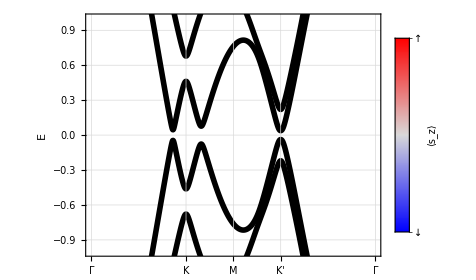

```mathematica
bandPlotWithWeight[Re@band2ddata,(*{"Γ","K","K'","Γ","M"}*){"Γ","K","M","K'","Γ"},loopfbz[[2]],AspectRatio->.7,PlotRange->{-1,1},ColorFunction->(Blend[{Blue,LightGray,Red},#]&),"LegendPosition"->{Left,Center},(*"LegendTickDigits"->{3,2}-1,*)PlotStyle->Directive[Thickness[.01]],LegendMarkerSize->150(*,Joined->False*),LegendLabel->"⟨s_z⟩","TickLabels"->{"↓","↑"}]
```

```mathematica
optionsselect[
Sequence[AspectRatio->.7,PlotRange->{-1,1},ColorFunction->(Blend[{Blue,LightGray,Red},#]&),"LegendPosition"->{Left,Center},"LegendTickDigits"->{3,2}(*-1*),PlotStyle->Directive[Thickness[.01]],LegendMarkerSize->150(*,Joined->False*),LegendLabel->"⟨s_z⟩", "TickLabels" -> {"-","+"}], 
BarLegend,
{"TickLabels"(*->{}*)}
]
```

Sequence[LegendMarkerSize→150,LegendLabel→⟨s_z⟩,TickLabels→{-,+}]